```mathematica
Charting`$InteractiveHighlighting=False
```

False

```mathematica
SetOptions[SelectedNotebook[],PrintingStyleEnvironment->"Printout",ShowSyntaxStyles->True]
```

```mathematica
n=25; (* Points to sample along each connection *)
```

```mathematica
path=N@With[{Γ={0,0,0},X={0,1,0},W={1/2,1,0},L={1/2,1/2,1/2},K={3/4,3/4,0},U={1/4,1,1/4}},{L,K,U,W,Γ,X,W,L,Γ,K,U,X}]; (* The list of high-symmetry points *)
kPts=Subdivide[#1,#2,n]&@@@Partition[path,2,1]//Flatten[#,1]&//DeleteAdjacentDuplicates;(* List of n points sampled along each line of the path going through the high-symmetry points, it's literally the points generated by traversing the line, although not in equal steps *)
Length@kPts (* Total count of the sampling points *)
Graphics3D[{Point[#]&/@kPts,Line[path]},Axes->True]
```

276

-Graphics3D-

```mathematica
basis=N@{{1,-1,1},{1,1,-1},{-1,1,1}}; (* The basis for the G *)
G=Tuples[Range[-5,5],3].basis; (* All possible combinations that give the G points *)
Length@G (* Number of sampled points *)
(* 1BZ represented for a bcc lattice *)
With[{G=Tuples[Range[-2,2],3].basis},Show[VoronoiMesh[G,PlotTheme->"Lines",MeshCellStyle->{{3,"Interior"}->Directive[Opacity[1]]}],Graphics3D[{{AbsolutePointSize[7],Red,Point[G]},{Thick,Line[path]}}],PlotRange->Automatic]]
```

1331

-Graphics3D-

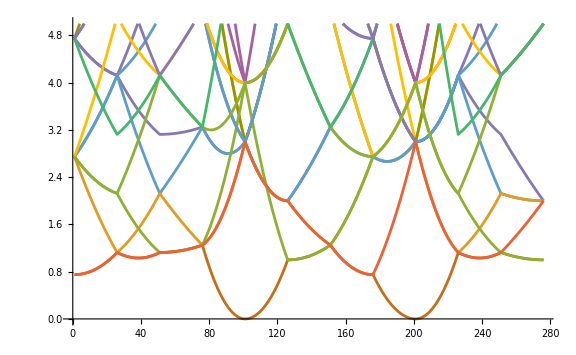

```mathematica
ens=With [{allCombs=Tuples[{kPts,G}]//Partition[#,Length@G]&},Norm[#1-#2]^2&@@@#&/@allCombs]//Transpose; (* Energy levels calculated along the path traced in the first Brillouin zone for a bcc lattice *)
ListLinePlot[ens,ImageSize->Large,PlotRange->{0,5}]
```

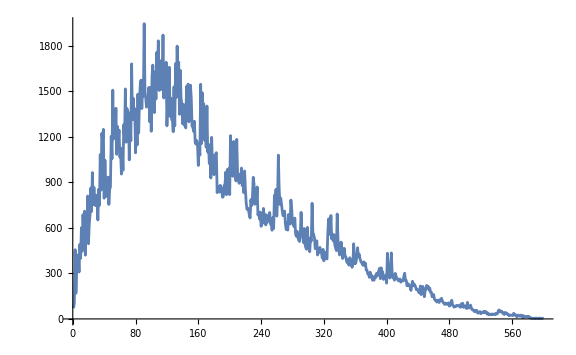

```mathematica
(* Density of states (only somes states) for the free electron *)
BinCounts[Flatten@ens,{0,300,0.5}]//ListLinePlot[#,ImageSize->Large,PlotRange->All]&
```

```mathematica
firstBz=With[{G=Tuples[Range[-1,1],3].basis},Select[MeshPrimitives[VoronoiMesh[G],3],RegionMember[#,{0,0,0}]&]//First];
```

```mathematica
kPts=RandomPoint[firstBz,10^4];
Graphics3D[{Style[firstBz,Opacity[0.7]],Point@kPts}]
RegionMeasure[firstBz]
```

-Graphics3D-

4.

```mathematica
eVals=With [{allCombs=Tuples[{kPts,G}]//Partition[#,Length@G]&},Norm[#1-#2]^2&@@@#&/@allCombs]//Transpose;
```

```mathematica
dos=BinCounts[Flatten@eVals,{0,50,0.5}];
```

```mathematica
dosFit=NonlinearModelFit[dos,a √x,{a},x];
dosFit[{"ANOVATable","ParameterTable"}]
```

{ | DF | SS | MS
Model | 1 | 1.54154×10^11 | 1.54154×10^11
Error | 99 | 1.16662×10^7 | 117841.
Uncorrected Total | 100 | 1.54166×10^11 | 
Corrected Total | 99 | 1.71188×10^10 | , | Estimate | Standard Error | t-Statistic | P-Value
a | 5525. | 4.83061 | 1143.75 | 8.14062×10^-206}

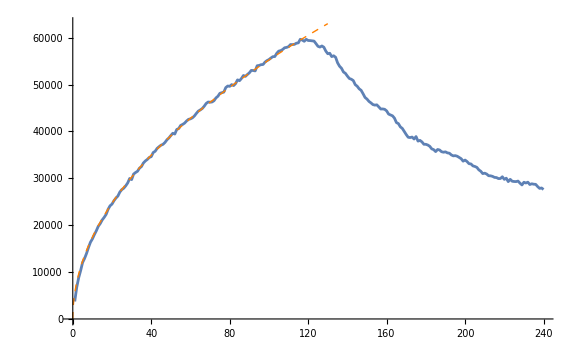

```mathematica
(* Plot of the density of states as a function of energy *)
Show[BinCounts[Flatten@eVals,{0,120,0.5}]//ListLinePlot[#,ImageSize->Large]&,Plot[dosFit["BestFit"],{x,0,130},PlotStyle->{Dashed,Orange,Thick}],PlotRange->All]
```

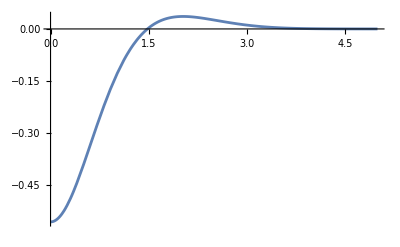

```mathematica
Plot[0.53706/2(r^2-2.19704)/(2.05716Exp[0.48716 r^2]-1),{r,0,5}]
```